## Author Informations

#### Author: A. C. Lehum Date: March 16, 2026 Filiation: Federal University of Pará Email: lehum@ufpa.br

# M. Gomes, A. C. Lehum and A. J. da Silva, ``On the physical running of the electric charge in a dimensionless theory of gravity,’’ [arXiv:2512.11742 [hep-th]].

## Preliminaries

```mathematica
description="Quantum electrodynamics coupled to Agravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
FAPatch[PatchModelsOnly->True];
```

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(2\)]\)";
```

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Agravity_QED","Agravity_QED"}],Model->FileNameJoin[{"Agravity_QED","Agravity_QED"}]};
```

## γ self-energy 1-loop

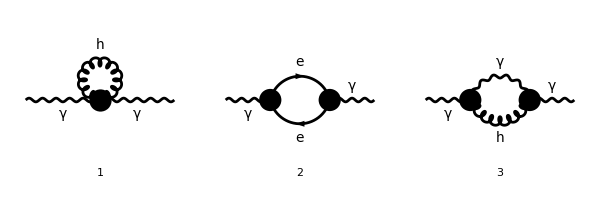

```mathematica
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
PhotonSelfEnergy=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1,ExcludeParticles->{S[1],S[2],F[2]}]&)[top1[1,1]];
Paint[PhotonSelfEnergy,ColumnsXRows->{5,1},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,200}];
```

Pure QED :

```mathematica
PhotonSelfEnergy[1]=FCFAConvert[CreateFeynAmp[DiagramExtract[PhotonSelfEnergy,{2}],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ}]/.{GaugeXi[T[2]]->1,m1-> IR,m2->IR,IR1-> IR,"κ"->1,Sqrt[GaugeXi[V[1]]]->1}//DiracSimplify
```

-(4 e^2 IR^2 g^μν)/((k^2-IR^2).((k-p)^2-IR^2))+(4 e^2 k^2 g^μν)/((k^2-IR^2).((k-p)^2-IR^2))-(4 e^2 g^μν (k·p))/((k^2-IR^2).((k-p)^2-IR^2))-(8 e^2 k^μ k^ν)/((k^2-IR^2).((k-p)^2-IR^2))+(4 e^2 k^ν p^μ)/((k^2-IR^2).((k-p)^2-IR^2))+(4 e^2 k^μ p^ν)/((k^2-IR^2).((k-p)^2-IR^2))

```mathematica
PhotonSelfEnergy[2]=TID[PhotonSelfEnergy[1],k,ToPaVe->True]/.{"κ"->1}//Simplify
```

(2 ⅈ π^2 e^2 (p^2 g^μν-p^μ p^ν) (2 (D-2) A_0(IR^2)-((D-2) p^2+4 IR^2) B_0(p^2,IR^2,IR^2)))/((D-1) p^2)

```mathematica
PhotonSelfEnergy[3]=PaXEvaluateUV[PhotonSelfEnergy[2],PaXImplicitPrefactor-> 1/(2 π)^D]//Simplify
```

(ⅈ e^2 (p^μ p^ν-p^2 g^μν))/(12 π^2 ε_UV)

Agravity corrections :

```mathematica
PhotonSelfEnergy[4]=FCFAConvert[CreateFeynAmp[DiagramExtract[PhotonSelfEnergy,{1,3}],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ}]/.{GaugeXi[T[2]]->1,m1-> IR,m2->IR,IR1-> IR,"κ"->1,Sqrt[GaugeXi[V[1]]]->1}//DiracSimplify
```

1/2 ⅈ ((f0^2 g^αγ g^βδ)/(3 (k^2-IR^2)^2)+(2 f0^2 k^α g^βδ k^γ)/(3 (k^2-IR^2)^3)+(2 f0^2 g^αγ k^β k^δ)/(3 (k^2-IR^2)^3)+(4 f0^2 k^α k^β k^γ k^δ)/(3 (k^2-IR^2)^4)-(f2^2 g^αδ g^βγ)/((k^2-IR^2)^2)+(2 f2^2 g^αγ g^βδ)/(3 (k^2-IR^2)^2)-(f2^2 g^αβ g^γδ)/((k^2-IR^2)^2)+(f2^2 k^α k^β g^γδ)/((k^2-IR^2)^3)+(ξ_(T(1)) k^α k^β g^γδ)/((k^2-IR^2)^3)-(2 f2^2 k^α g^βδ k^γ)/(3 (k^2-IR^2)^3)+(f2^2 g^αδ k^β k^γ)/((k^2-IR^2)^3)+(ξ_(T(1)) g^αδ k^β k^γ)/((k^2-IR^2)^3)+(f2^2 k^α g^βγ k^δ)/((k^2-IR^2)^3)+(ξ_(T(1)) k^α g^βγ k^δ)/((k^2-IR^2)^3)-(2 f2^2 g^αγ k^β k^δ)/(3 (k^2-IR^2)^3)+(f2^2 g^αβ k^γ k^δ)/((k^2-IR^2)^3)+(ξ_(T(1)) g^αβ k^γ k^δ)/((k^2-IR^2)^3)-(4 f2^2 k^α k^β k^γ k^δ)/(3 (k^2-IR^2)^4)) (-1/4 ⅈ p^μ p^ν g^αδ g^βγ+1/4 ⅈ p^μ g^νδ p^α g^βγ+1/4 ⅈ g^μδ p^ν p^α g^βγ+1/4 ⅈ p^μ g^να p^δ g^βγ+1/4 ⅈ g^μα p^ν p^δ g^βγ-1/2 ⅈ g^μν p^α p^δ g^βγ-1/4 ⅈ g^μδ g^να p^2 g^βγ-1/4 ⅈ g^μα g^νδ p^2 g^βγ+1/4 ⅈ g^μν g^αδ p^2 g^βγ+1/4 ⅈ p^μ p^ν g^αγ g^βδ-1/4 ⅈ p^μ g^νγ p^α g^βδ-1/4 ⅈ g^μγ p^ν p^α g^βδ-1/4 ⅈ p^μ g^νδ g^αγ p^β-1/4 ⅈ g^μδ p^ν g^αγ p^β+1/4 ⅈ p^μ g^νγ g^αδ p^β+1/4 ⅈ g^μγ p^ν g^αδ p^β+1/4 ⅈ g^μδ g^νγ p^α p^β+1/4 ⅈ g^μγ g^νδ p^α p^β-1/4 ⅈ p^μ p^ν g^αβ g^γδ+1/4 ⅈ p^μ g^νβ p^α g^γδ+1/4 ⅈ g^μβ p^ν p^α g^γδ+1/4 ⅈ p^μ g^να p^β g^γδ+1/4 ⅈ g^μα p^ν p^β g^γδ-1/2 ⅈ g^μν p^α p^β g^γδ+1/4 ⅈ p^μ g^νδ g^αβ p^γ+1/4 ⅈ g^μδ p^ν g^αβ p^γ+1/4 ⅈ p^μ g^νβ g^αδ p^γ+1/4 ⅈ g^μβ p^ν g^αδ p^γ-1/2 ⅈ g^μδ g^νβ p^α p^γ-1/2 ⅈ g^μβ g^νδ p^α p^γ-1/4 ⅈ p^μ g^να g^βδ p^γ-1/4 ⅈ g^μα p^ν g^βδ p^γ+1/2 ⅈ g^μν p^α g^βδ p^γ+1/4 ⅈ g^μδ g^να p^β p^γ+1/4 ⅈ g^μα g^νδ p^β p^γ-1/2 ⅈ g^μν g^αδ p^β p^γ+1/4 ⅈ p^μ g^νγ g^αβ p^δ+1/4 ⅈ g^μγ p^ν g^αβ p^δ-1/4 ⅈ p^μ g^νβ g^αγ p^δ-1/4 ⅈ g^μβ p^ν g^αγ p^δ+1/4 ⅈ g^μγ g^νβ p^α p^δ+1/4 ⅈ g^μβ g^νγ p^α p^δ-1/2 ⅈ g^μγ g^να p^β p^δ-1/2 ⅈ g^μα g^νγ p^β p^δ+1/2 ⅈ g^μν g^αγ p^β p^δ+1/4 ⅈ g^μβ g^να p^γ p^δ+1/4 ⅈ g^μα g^νβ p^γ p^δ-1/2 ⅈ g^μν g^αβ p^γ p^δ-1/4 ⅈ g^μδ g^νγ g^αβ p^2-1/4 ⅈ g^μγ g^νδ g^αβ p^2+1/4 ⅈ g^μδ g^νβ g^αγ p^2+1/4 ⅈ g^μβ g^νδ g^αγ p^2-1/4 ⅈ g^μγ g^νβ g^αδ p^2-1/4 ⅈ g^μβ g^νγ g^αδ p^2+1/4 ⅈ g^μγ g^να g^βδ p^2+1/4 ⅈ g^μα g^νγ g^βδ p^2-1/4 ⅈ g^μν g^αγ g^βδ p^2-1/4 ⅈ g^μβ g^να g^γδ p^2-1/4 ⅈ g^μα g^νβ g^γδ p^2+1/4 ⅈ g^μν g^αβ g^γδ p^2)+((f0^2 g^αγ g^βδ g^ξχ)/(3 ((k-p)^2-IR^2).(k^2-IR^2)^2)+(2 f0^2 k^α g^βδ k^γ g^ξχ)/(3 (k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(2 f0^2 g^αγ k^β k^δ g^ξχ)/(3 (k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(4 f0^2 k^α k^β k^γ k^δ g^ξχ)/(3 ((k-p)^2-IR^2).(k^2-IR^2)^4)+(f0^2 (1-ξ_(V(1))) g^αγ g^βδ (k-p)^ξ (p-k)^χ)/(3 ((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(2 f0^2 (1-ξ_(V(1))) k^α g^βδ k^γ (k-p)^ξ (p-k)^χ)/(3 (k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(2 f0^2 (1-ξ_(V(1))) g^αγ k^β k^δ (k-p)^ξ (p-k)^χ)/(3 (k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(4 f0^2 (1-ξ_(V(1))) k^α k^β k^γ k^δ (k-p)^ξ (p-k)^χ)/(3 ((k-p)^2-IR^2)^2.(k^2-IR^2)^4)-(f2^2 g^αδ g^βγ g^ξχ)/(((k-p)^2-IR^2).(k^2-IR^2)^2)+(2 f2^2 g^αγ g^βδ g^ξχ)/(3 ((k-p)^2-IR^2).(k^2-IR^2)^2)-(f2^2 g^αβ g^γδ g^ξχ)/(((k-p)^2-IR^2).(k^2-IR^2)^2)+(f2^2 k^α k^β g^γδ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(ξ_(T(1)) k^α k^β g^γδ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)-(2 f2^2 k^α g^βδ k^γ g^ξχ)/(3 (k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(f2^2 g^αδ k^β k^γ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(ξ_(T(1)) g^αδ k^β k^γ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(f2^2 k^α g^βγ k^δ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(ξ_(T(1)) k^α g^βγ k^δ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)-(2 f2^2 g^αγ k^β k^δ g^ξχ)/(3 (k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(f2^2 g^αβ k^γ k^δ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)+(ξ_(T(1)) g^αβ k^γ k^δ g^ξχ)/((k^2-IR^2).((k-p)^2-IR^2).(k^2-IR^2)^2)-(4 f2^2 k^α k^β k^γ k^δ g^ξχ)/(3 ((k-p)^2-IR^2).(k^2-IR^2)^4)+(2 f2^2 (1-ξ_(V(1))) g^αγ g^βδ (k-p)^ξ (p-k)^χ)/(3 ((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(f2^2 (1-ξ_(V(1))) k^α k^β g^γδ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(ξ_(T(1)) (1-ξ_(V(1))) k^α k^β g^γδ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)-(2 f2^2 (1-ξ_(V(1))) k^α g^βδ k^γ (k-p)^ξ (p-k)^χ)/(3 (k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(f2^2 (1-ξ_(V(1))) g^αδ k^β k^γ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(ξ_(T(1)) (1-ξ_(V(1))) g^αδ k^β k^γ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(f2^2 (1-ξ_(V(1))) k^α g^βγ k^δ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(ξ_(T(1)) (1-ξ_(V(1))) k^α g^βγ k^δ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)-(2 f2^2 (1-ξ_(V(1))) g^αγ k^β k^δ (k-p)^ξ (p-k)^χ)/(3 (k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(f2^2 (1-ξ_(V(1))) g^αβ k^γ k^δ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(ξ_(T(1)) (1-ξ_(V(1))) g^αβ k^γ k^δ (k-p)^ξ (p-k)^χ)/((k^2-IR^2).((k-p)^2-IR^2)^2.(k^2-IR^2)^2)-(4 f2^2 (1-ξ_(V(1))) k^α k^β k^γ k^δ (k-p)^ξ (p-k)^χ)/(3 ((k-p)^2-IR^2)^2.(k^2-IR^2)^4)+(f2^2 (1-ξ_(V(1))) g^αδ g^βγ (p-k)^ξ (p-k)^χ)/(((k-p)^2-IR^2)^2.(k^2-IR^2)^2)+(f2^2 (1-ξ_(V(1))) g^αβ g^γδ (p-k)^ξ (p-k)^χ)/(((k-p)^2-IR^2)^2.(k^2-IR^2)^2)) (1/2 ⅈ (k-p)^μ p^α g^γξ-1/2 ⅈ g^μα ((k-p)·p) g^γξ-1/2 ⅈ g^μξ p^α (k-p)^γ+1/2 ⅈ (k-p)^μ g^αξ p^γ-1/2 ⅈ g^μξ (k-p)^α p^γ-1/2 ⅈ (k-p)^μ g^αγ p^ξ+1/2 ⅈ g^μγ (k-p)^α p^ξ+1/2 ⅈ g^μα (k-p)^γ p^ξ+1/2 ⅈ g^μξ g^αγ ((k-p)·p)-1/2 ⅈ g^μγ g^αξ ((k-p)·p)) (-1/2 ⅈ (p-k)^ν p^β g^δχ+1/2 ⅈ g^νβ (p·(p-k)) g^δχ-1/2 ⅈ (p-k)^ν g^βχ p^δ+1/2 ⅈ g^νχ (p-k)^β p^δ+1/2 ⅈ g^νχ p^β (p-k)^δ+1/2 ⅈ (p-k)^ν g^βδ p^χ-1/2 ⅈ g^νδ (p-k)^β p^χ-1/2 ⅈ g^νβ (p-k)^δ p^χ-1/2 ⅈ g^νχ g^βδ (p·(p-k))+1/2 ⅈ g^νδ g^βχ (p·(p-k)))

```mathematica
PhotonSelfEnergy[5]=TID[PhotonSelfEnergy[4],k,ToPaVe->True]/.{"κ"->1}//Simplify
```

1/(48 (D-1) D p^2)ⅈ π^2 (p^μ p^ν-g^μν p^2) (16 D f0^2 p^2 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^6-16 D f2^2 p^2 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^6-4 D^2 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) IR^4+8 D f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) IR^4+4 D^2 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) IR^4-8 D f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) IR^4+4 D^2 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) IR^4-8 D f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) IR^4-4 D^2 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) IR^4+8 D f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) IR^4-12 D^2 f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+16 D f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+12 D^2 f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^2 IR^4-16 D f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+8 D^2 f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+48 D f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+88 D^2 f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^2 IR^4-192 D f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^2 IR^4+96 D^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^4-144 D D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^4+36 D^2 f0^2 p^4 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^4-72 D f0^2 p^4 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^4-36 D^2 f2^2 p^4 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^4+72 D f2^2 p^4 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^4+24 D^2 f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-64 D f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+32 f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-24 D^2 f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+64 D f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-32 f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+12 D^3 f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-56 D^2 f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+64 D f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-12 D^3 f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+92 D^2 f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2-136 D f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^4 IR^2+36 D^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^4 IR^2-72 D D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^4 IR^2-4 D^3 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2+40 D^2 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2-128 D f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2+96 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2+28 D^3 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2-148 D^2 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2+200 D f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2-96 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^2 IR^2-4 D^3 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2+8 D^2 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2+64 D f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2+16 D^3 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2-200 D^2 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2+320 D f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^2 IR^2+24 D^3 C_0(0,0,0,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^2-108 D^2 C_0(0,0,0,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^2+72 D C_0(0,0,0,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^2+72 D^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^2-96 D C_0(0,p^2,p^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^2 IR^2-24 D^2 f0^2 p^6 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^2+48 D f0^2 p^6 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^2+24 D^2 f2^2 p^6 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^2-48 D f2^2 p^6 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2) IR^2-4 D^2 f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^6+8 D f0^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^6+4 D^2 f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^6-8 D f2^2 D_0(0,0,0,0,0,0,IR^2,IR^2,IR^2,IR^2) p^6-4 D^3 f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6+16 D^2 f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6-16 D f0^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6+4 D^3 f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6-28 D^2 f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6+40 D f2^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) p^6-12 D^2 D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^6+24 D D_0(0,0,p^2,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^6+4 D^3 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4-12 D^2 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4-8 D f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4+32 f0^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4-4 D^3 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4+24 D^2 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4-16 D f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4-32 f2^2 C_0(0,0,0,IR^2,IR^2,IR^2) p^4+D^4 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4-2 D^3 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4-12 D^2 f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4+24 D f0^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4+2 D^4 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4-46 D^3 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4+216 D^2 f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4-264 D f2^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) p^4+12 D^2 C_0(0,0,0,IR^2,IR^2,IR^2) ξ_(T(1)) p^4-24 D C_0(0,0,0,IR^2,IR^2,IR^2) ξ_(T(1)) p^4+24 D^2 C_0(0,p^2,p^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^4-48 D C_0(0,p^2,p^2,IR^2,IR^2,IR^2) ξ_(T(1)) p^4-2 (D-2) D B_0(p^2,IR^2,IR^2) (2 ((D-4) f0^2-(D-7) f2^2) IR^2+((D^2-6 D+8) f0^2+2 (D^2-18 D+47) f2^2) p^2+6 ξ_(T(1)) (IR^2+p^2))+B_0(0,IR^2,IR^2) (4 (D-2) D ((D-4) f0^2-(D-7) f2^2) IR^2+((D^4-8 D^3+36 D^2-104 D+96) f0^2-2 (5 D^4-37 D^3+108 D^2-136 D+48) f2^2) p^2+12 D ξ_(T(1)) ((D-2) IR^2+(2 D^2-9 D+6) p^2))+4 D^2 f0^2 p^8 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2)-8 D f0^2 p^8 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2)-4 D^2 f2^2 p^8 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2)+8 D f2^2 p^8 E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2))

```mathematica
PhotonSelfEnergy[6]=PaXEvaluateUV[PhotonSelfEnergy[5],PaXImplicitPrefactor-> 1/(2 π)^D]//Simplify
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {E_0(0,0,0,p^2,p^2,0,0,p^2,0,p^2,IR^2,IR^2,IR^2,IR^2,IR^2)}

0